```mathematica
Clear["Global`*"]
```

```mathematica
fk[a_,b_,u1_,u2_,α_,β_]:=(a b Sqrt[1+Abs[β]^2] (-2 E^((1+a) Sqrt[α]) (E^u1-E^u2) β ((-1+a) E^(u1+2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α])+(-1+a) E^(u1+2 b Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α])-2 (-1+a) b E^(u1+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α]+(-1+a) E^(u2+2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β+(-1+a) E^(u2+2 b Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) β-2 (-1+a) b E^(u2+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+(-1+a) E^(2 b Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)-(-1+a) E^(2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+2 (a-b) E^(u1+u2+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] (1+β)) Sqrt[α/(1+Abs[β]^2)]+1/(Sqrt[1+Abs[β]^2]) (E^(2 u1+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u1+(1+a) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u2+(1+a) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u1+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u2+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u1+(a+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u2+(a+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+2 b E^(2 u1+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-4 b E^(u1+u2+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+2 b E^(2 u2+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u1+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+4 b E^(u1+u2+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u2+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-E^(u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)+E^(u2+2 (a+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)-E^(u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(2 u1+u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(u2+2 (1+a) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (a+b) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(2 u1+u2+2 (1+a) Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(u1+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+E^(u1+2 (a+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+E^(u1+2 (u2+(a+b) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+2 u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(u1+2 (1+a) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+2 (u2+(1+a) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(u1+2 (u2+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+2 E^(u1+u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+(-1+b Sqrt[α]) β-β^2)+2 E^(u1+u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β+β^2)+2 E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β+a Sqrt[α] β+β^2)+2 E^(u1+u2+2 (a+b) Sqrt[α]) (1+β-b Sqrt[α] β+β^2+a (-Sqrt[α] β+b α (1+β+β^2))))+β (2 E^((1+a) Sqrt[α]) (E^u1-E^u2) ((-1+a) E^(u1+2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α])+(-1+a) E^(u1+2 b Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α])-2 (-1+a) b E^(u1+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α]+(-1+a) E^(u2+2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β+(-1+a) E^(u2+2 b Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) β-2 (-1+a) b E^(u2+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+(-1+a) E^(2 b Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)-(-1+a) E^(2 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+2 (a-b) E^(u1+u2+(a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] (1+β)) Sqrt[α/(1+Abs[β]^2)]+1/(Sqrt[1+Abs[β]^2]) (E^(2 u1+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u1+(1+a) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u2+(1+a) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u1+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β-E^(2 (u2+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u1+(a+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u2+(a+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β+2 b E^(2 u1+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-4 b E^(u1+u2+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+2 b E^(2 u2+(2+a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u1+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β+4 b E^(u1+u2+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u2+(3 a+b) Sqrt[α]) (1+b Sqrt[α]) Sqrt[α] β-E^(u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)+E^(u2+2 (a+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) (1+β)-E^(u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(2 u1+u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(u2+2 (1+a) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (a+b) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(2 u1+u2+2 (1+a) Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(u1+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+E^(u1+2 (a+b) Sqrt[α]) (1+a Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+E^(u1+2 (u2+(a+b) Sqrt[α])) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+2 u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(u1+2 (1+a) Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)-E^(u1+2 (u2+(1+a) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(u1+2 (u2+(1+b) Sqrt[α])) (1+a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+2 E^(u1+u2+2 (1+b) Sqrt[α]) (1+a Sqrt[α]) (-1+(-1+b Sqrt[α]) β-β^2)+2 E^(u1+u2+4 a Sqrt[α]) (-1+a Sqrt[α]) (1+b Sqrt[α]) (1+β+β^2)+2 E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β+a Sqrt[α] β+β^2)+2 E^(u1+u2+2 (a+b) Sqrt[α]) (1+β-b Sqrt[α] β+β^2+a (-Sqrt[α] β+b α (1+β+β^2)))))))/((1+β) (-2 a^3 b (E^u1-E^u2)^2 (E^((2+a+b) Sqrt[α])+E^((3 a+b) Sqrt[α])) α β+b (-1+E^u1) (-1+E^u2) (1+β) (E^(u2+2 (a+b) Sqrt[α]) (1-b Sqrt[α])+E^(u2+2 (1+b) Sqrt[α]) (-1+b Sqrt[α])-E^(u2+4 a Sqrt[α]) (1+b Sqrt[α])+E^(u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α])+E^(u1+2 (1+b) Sqrt[α]) (-1+b Sqrt[α]) β-E^(u1+4 a Sqrt[α]) (1+b Sqrt[α]) β+E^(u1+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) β+E^(u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(u1+u2+2 (1+b) Sqrt[α]) (1+b Sqrt[α]) (1+β)-E^(u1+u2+2 (a+b) Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(u1+2 (a+b) Sqrt[α]) (β-b Sqrt[α] β))+a^2 Sqrt[α] (2 b E^(2 u1+(2+a+b) Sqrt[α]) (-1+Sqrt[α]) β-4 b E^(u1+u2+(2+a+b) Sqrt[α]) (-1+Sqrt[α]) β+2 b E^(2 u2+(2+a+b) Sqrt[α]) (-1+Sqrt[α]) β+2 b E^(2 u1+(3 a+b) Sqrt[α]) (1+Sqrt[α]) β-4 b E^(u1+u2+(3 a+b) Sqrt[α]) (1+Sqrt[α]) β+2 b E^(2 u2+(3 a+b) Sqrt[α]) (1+Sqrt[α]) β-2 b E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) β+E^(2 (u1+(1+a) Sqrt[α])) (1+b Sqrt[α]) (-1+b-β) β+E^(2 (u1+(1+b) Sqrt[α])) (-1+b^2 Sqrt[α]+b (-1+Sqrt[α] (-1+β))-β) β-E^(2 (u1+(a+b) Sqrt[α])) (-1-b^2 Sqrt[α]+b (1+Sqrt[α] (-1+β))-β) β-(1+b) E^(u2+2 (1+b) Sqrt[α]) (-1+b Sqrt[α]) (1+β)+(1+b) E^(u2+2 (a+b) Sqrt[α]) (-1+b Sqrt[α]) (1+β)-(1+b) E^(u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β)+(1+b) E^(u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β)-(1+b) E^(2 u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β)+E^(2 u1+u2+2 (a+b) Sqrt[α]) (1+b^2 Sqrt[α]+b (1+Sqrt[α] (1-2 β))) (1+β)-(1+b) E^(u1+2 (1+b) Sqrt[α]) (-1+b Sqrt[α]) β (1+β)+(1+b) E^(u1+2 (a+b) Sqrt[α]) (-1+b Sqrt[α]) β (1+β)-(1+b) E^(u1+2 (u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) β (1+β)-(1+b) E^(u1+4 a Sqrt[α]) (1+b Sqrt[α]) β (1+β)+(1+b) E^(u1+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) β (1+β)+E^(2 (u1+u2+2 a Sqrt[α])) (1+b Sqrt[α]) (1+β)^2+E^(2 (u1+u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) (1+β)^2-E^(2 (u1+u2+(1+b) Sqrt[α])) (1+b Sqrt[α]) (1+β)^2-E^(2 (u1+u2+(a+b) Sqrt[α])) (1+b Sqrt[α]) (1+β)^2+E^(2 u1+4 a Sqrt[α]) (1+b Sqrt[α]) β (1+b+β)-E^(2 u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β) (1+b+2 β)+E^(2 u1+u2+2 (1+b) Sqrt[α]) (1+β) (1+b+b Sqrt[α]+b^2 Sqrt[α]+2 β)+E^(2 (u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) (-1+(-1+b) β)+E^(2 u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β+b β)-E^(u1+2 u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β) (2+β+b β)+E^(u1+2 (u2+(1+b) Sqrt[α])) (1+β) (2+(1+b) (1+b Sqrt[α]) β)+E^(2 (u2+(a+b) Sqrt[α])) (1+b (Sqrt[α] (-1+β)-β)+β+b^2 Sqrt[α] β)+E^(u1+2 (u2+(a+b) Sqrt[α])) (1+β) (β+b^2 Sqrt[α] β+b (Sqrt[α] (-2+β)+β))+E^(2 (u2+(1+b) Sqrt[α])) (-1-β+b^2 Sqrt[α] β-b (Sqrt[α] (-1+β)+β))+2 E^(u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) ((1+β)^2+b (1+β+β^2))-2 E^(u1+u2+2 (1+b) Sqrt[α]) (b^2 Sqrt[α] β+(1+β)^2+b (1+β-2 Sqrt[α] β+β^2))+2 b E^(u1+u2+2 (a+b) Sqrt[α]) (β+Sqrt[α] (1+β^2+b (1+β+β^2))))-a (E^(2 (u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) (-1+b (Sqrt[α] (-1+β)-β)-β)-2 b E^(2 u1+(2+a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β+4 b E^(u1+u2+(2+a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β-2 b E^(2 u2+(2+a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β+2 b E^(2 u1+(3 a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β-4 b E^(u1+u2+(3 a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β+2 b E^(2 u2+(3 a+b) Sqrt[α]) (2+b Sqrt[α]) Sqrt[α] β-E^(u2+2 (1+b) Sqrt[α]) (1+b-2 b Sqrt[α]+b^2 (-Sqrt[α]+α)) (1+β)+E^(u2+2 (a+b) Sqrt[α]) (1+b-2 b Sqrt[α]+b^2 (-Sqrt[α]+α)) (1+β)-E^(u2+4 a Sqrt[α]) (1+b+2 b Sqrt[α]+b^2 (Sqrt[α]+α)) (1+β)+E^(u2+2 (1+a) Sqrt[α]) (1+b+2 b Sqrt[α]+b^2 (Sqrt[α]+α)) (1+β)-E^(u1+2 (1+b) Sqrt[α]) (1+b-2 b Sqrt[α]+b^2 (-Sqrt[α]+α)) β (1+β)+E^(u1+2 (a+b) Sqrt[α]) (1+b-2 b Sqrt[α]+b^2 (-Sqrt[α]+α)) β (1+β)-E^(u1+4 a Sqrt[α]) (1+b+2 b Sqrt[α]+b^2 (Sqrt[α]+α)) β (1+β)+E^(u1+2 (1+a) Sqrt[α]) (1+b+2 b Sqrt[α]+b^2 (Sqrt[α]+α)) β (1+β)+E^(2 (u1+u2+2 a Sqrt[α])) (1+b Sqrt[α])^2 (1+β)^2-E^(2 (u1+u2+(a+b) Sqrt[α])) (1+b Sqrt[α])^2 (1+β)^2+E^(2 (u1+u2+(1+a) Sqrt[α])) (-1+b^2 α) (1+β)^2-E^(2 (u1+u2+(1+b) Sqrt[α])) (-1+b^2 α) (1+β)^2-E^(2 (u1+(1+a) Sqrt[α])) (1+b Sqrt[α]) β (1+b (1+Sqrt[α] (-1+β))+β)-E^(2 (u1+(a+b) Sqrt[α])) β (1+b (1-2 Sqrt[α] (-1+β))+b^2 (-Sqrt[α]+α (-1+β))+β)+E^(2 u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) (1+β) (1+b-b Sqrt[α]+2 β)-E^(u1+2 (u2+(1+a) Sqrt[α])) (1+b Sqrt[α]) (1+β) (-2+(-1+b (-1+Sqrt[α])) β)+E^(u1+2 (u2+(1+b) Sqrt[α])) (1+β) (-2+b (2 Sqrt[α]-β)-β+b^2 (-Sqrt[α]+α) β)+E^(u1+2 (u2+(a+b) Sqrt[α])) (1+b Sqrt[α]) (1+β) (2+β+b (Sqrt[α] (-2+β)+β))+E^(2 (u2+(a+b) Sqrt[α])) (-1-β-b (2 Sqrt[α] (-1+β)+β)+b^2 (α (-1+β)+Sqrt[α] β))+E^(2 u1+u2+2 (1+b) Sqrt[α]) (1+β) (-1+b^2 (-Sqrt[α]+α)-2 β+b (-1+2 Sqrt[α] β))+E^(2 (u1+(1+b) Sqrt[α])) β (1+b+β-2 b Sqrt[α] β+b^2 (-Sqrt[α]+α+α β))+E^(2 (u2+(1+b) Sqrt[α])) (1+β+b (-2 Sqrt[α]+β)+b^2 (α-Sqrt[α] β+α β))-2 E^(u1+u2+2 (1+a) Sqrt[α]) (1+b Sqrt[α]) ((1+β)^2+b (1+β+2 Sqrt[α] β+β^2))+2 E^(u1+u2+2 (a+b) Sqrt[α]) (-(1+β)^2-b (1+β-4 Sqrt[α] β+β^2)+b^2 (α-Sqrt[α] β+α β^2))+E^(2 u1+4 a Sqrt[α]) (1+b Sqrt[α]) β (1+β+b (1+Sqrt[α] (1+β)))+E^(2 u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β+b (β+Sqrt[α] (1+β)))+2 E^(u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) ((1+β)^2+b (1+β+β^2+Sqrt[α] (1+β)^2))-E^(u1+2 u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β) (2+β+b (β+Sqrt[α] (2+β)))-E^(2 u1+u2+2 (a+b) Sqrt[α]) (1+b Sqrt[α]) (1+β) (-1-2 β+b (-1+Sqrt[α] (-1+2 β)))-E^(2 u1+u2+4 a Sqrt[α]) (1+b Sqrt[α]) (1+β) (1+2 β+b (1+Sqrt[α] (1+2 β)))+2 E^(u1+u2+2 (1+b) Sqrt[α]) (b^2 Sqrt[α] β+(1+β)^2+b (1+β+β^2-Sqrt[α] (1+4 β+β^2))))))
```

```mathematica
d=1;
U01=-4;
U02=0;
a=3;
b=1;
nmax = 6;
Rsink=1;
Rmax=25;
t0=0;
t1=1000;
wmin=-3
wmax=3
datapoints =12;
u1[r_]:=U01 Exp[-((r-a)/b)^n];
u2[r_]:=U02 Exp[-((r-a)/b)^n];
pde = {D[ρ1[r,t],t]==2/r ρ1[r,t] u1'[r]+D[ρ1[r,t],r]u1'[r]+ρ1[r,t] u1''[r]+d 2/r D[ρ1[r,t],r]+d D[ρ1[r,t],r,r]-w12 ρ1[r,t] + w21 ρ2[r,t],
D[ρ2[r,t],t]==2/r ρ2[r,t] u2'[r]+D[ρ2[r,t],r]u2'[r]+ρ2[r,t] u2''[r]+d 2/r D[ρ2[r,t],r]+d D[ρ2[r,t],r,r]-w21 ρ2[r,t] + w12 ρ1[r,t]
};
bc = {
ρ1[Rsink,t]==0,
ρ2[Rsink,t]==0,
ρ1[Rmax,t]==w21/(w12+w21),
ρ2[Rmax,t]==w12/(w12+w21)
};
ic = {
ρ1[r,t0]==w21/(w12+w21)*(1-1/r),
ρ2[r,t0]==w12/(w12+w21)*(1-1/r)
};
```

```mathematica
Densities=Table[0,{k,1,3},{i,1,datapoints+1},{j,1,nmax}];
ReactionRate=Table[0,{k,1,2},{i,1,datapoints+1},{j,1,nmax}];
Densities2=Table[0,{k,1,3},{i,1,datapoints+1},{j,1,nmax}];
ReactionRate2=Table[0,{k,1,2},{i,1,datapoints+1},{j,1,nmax}];
```

```mathematica
For[j=1,j≤nmax,j++,
n=2^j;
For[i=0,i<=datapoints,i++,
w21=1;
w12=10^(-wmin+(wmin+wmax)*i/datapoints);
sol=NDSolve[{pde,bc,ic},{ρ1,ρ2},{t,t0,t1},{r,Rsink,Rmax},MaxSteps->Infinity,MaxStepFraction->0.002,AccuracyGoal->15,StartingStepSize->0.001,WorkingPrecision->MachinePrecision,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->10000}}];
Print["Done","j=",j,"i=",i,"w12=",N[w12],"w21=",N[w21]];
ρ1eq[r_]=ρ1[r,t1]/.sol;
ρ2eq[r_]=ρ2[r,t1]/.sol;
ρtot[r_]=(ρ1[r,t1]+ρ2[r,t1])/.sol;

Densities[[1,i+1,j]]=ρ1eq[r];
Densities[[2,i+1,j]]=ρ2eq[r];
Densities[[3,i+1,j]]=ρtot[r];
ReactionRate[[1,i+1,j]]=w12;
ReactionRate[[2,i+1,j]]=D[ρtot[r],r]/.r->1;
]]
```

```mathematica
a=Table[0,{i,1,nmax}];
```

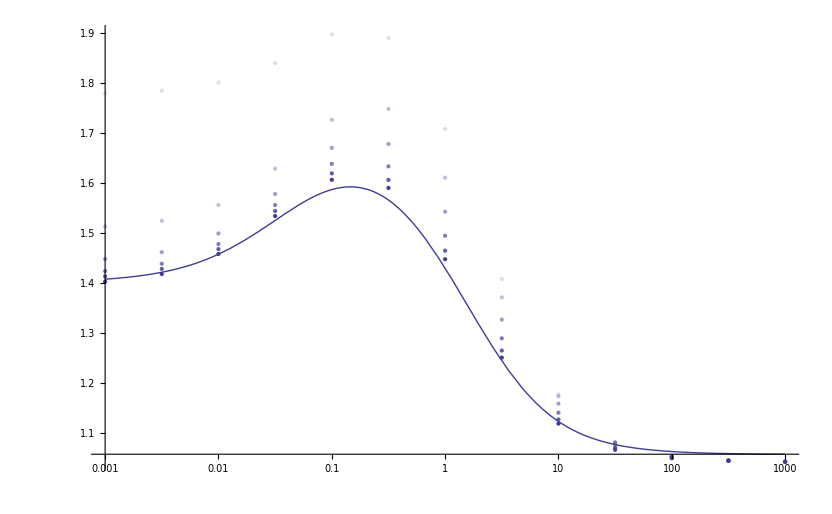

```mathematica
p=Table[{},{j,1,nmax}];
For[j=1,j≤nmax,j++,
a=N[Partition[Flatten[Transpose[ReactionRate[[All,All,j]]]],2]];
p[[j]]=ListLogLinearPlot[{a},PlotRange->All,PlotStyle->Opacity[j/nmax]];
]
w21=1;
at=2;
bt=4;
u1=-4;
u2=0;
w21=1;
pa = LogLinearPlot[fk[at,bt,U01,U02,Abs[-w12-w21],w21/w12],{w12,10^(-3),10^(3)},PlotRange->All];
Show[pa,p,PlotRange->All]
```

```mathematica
b=Table[0,{i,1,nmax+1}];
b[[1]]=N[ReactionRate[[1,All,1]]];
For[j=1,j≤nmax,j++,
b[[j+1]]=N[0.945901*Flatten[ReactionRate[[2,All,j]]]];
]
Export["numeric_rates.csv",Transpose[b]];
```

```mathematica
resolution=1000;
c=Table[{N[10^w12],fk[at,bt,U01,U02,Abs[-10^w12-w21],w21/10^w12]},{w12,wmin,wmax,(wmax-wmin)/resolution}];
Export["analytic_rates.csv",N[c]]
```

```mathematica
resolution=100
Umin=-4;
Umax=4;
usteps=Umax-Umin;
d=Table[0,{i,1,usteps/2+2}];
d[[1]]=Table[N[10^w12],{w12,wmin,wmax,(wmax-wmin)/resolution}];
For[i=Umin,i≤Umax,i+=2,
U01=i;
Print[i/2-Umin/2+2];
d[[i/2-Umin/2+2]]=Flatten[Table[N[fk[at,bt,U01,U02,Abs[-10^w12-w21],w21/10^w12]],{w12,wmin,wmax,(wmax-wmin)/resolution}]];
]
Export["analytic_rates_for_var_U01.csv",Transpose[d]]
```

100

2

3

4

5

6

analytic_rates_for_var_U01.csv